```mathematica
(* -- FUNDAMENTALS -- *)
```

```mathematica
(* All variable definitions are global rules *)
(* Variable declarations are just symbols that go into symbol table and referenced from there *)
(* Definitions for symbols are rules called OwnValues and stored in OwnValues[symbol] *)
(* Mathematica is a dynamically typed language, the var is inferred when defined *)
```

```mathematica
[]      (* square brackets for args instead of round brackets as for C/C++ *)
[[]]  (* double square brackets act as at() for lists or Part for expressions *)
{}      (* curly brackets for lists *)
()      (* only to group arithmetic expressions *)
```

```mathematica
,  (* to separate items in a list *)
;  (* compound expression in the case.. a=3; b=2; a+b *)
;  (* do not print the output.. 2/3; *)
```

```mathematica
%     (* the last result generated *)
%%   (* the next-to-last result.. %%% etc.. *)
%n  (* the result on output line *)
```

```mathematica
=   (* set, assignment operator *)
 := (* SetDelayed.. assign rhs to be the delayed value of lhs.. 
when lhs appears,it is replaced by rhs,evaluated afresh each time *)
=. (* unset a variable x=. *)
== (* comparison operator *)
  === (* SameQ, compares syntatic form instead of value *)
 Equal (* returns true if lhs and rhs are identical *)
/;(*conditional operator.. f[x_]:=ppp[x]/;x>0 .. x needs to be positive*)
/@ (*map operator*)
```

```mathematica
f[x_]:=x^2;
r:= RandomReal[] ;
g=RandomInteger[2,5];
{r,r,r}
{g,g,g}
```

SetDelayed::write: Tag Real in 0.2[x_] is Protected.

{0.875465,0.35885,0.453209}

{{0,0,0,2,2},{0,0,0,2,2},{0,0,0,2,2}}

```mathematica
Clear[a];                            (* clears variables, ie. removes the rules associated with a symbol *)
ClearAll["Global`*"]    (* clears all variables *)
Remove["Global'*"]         (* clears all variables and remove all symbols *)
=.                                           (* clear a composite variable a[b][1]=. *)
Quit[]                                   (* terminate the language kernel *)(*Alt+. abort cell computation*)
```

```mathematica
Clear[a];
a=10;
ValueQ[a]  (* check 'a' has a value.. if it has an lhs of some global rule *)
a=.              (* clear the lhs rule *)
ValueQ[a]
```

True

False

```mathematica
N[1/2]       (* returns the numerical value of the expr *)
1/2 //N   (* same as above *)
```

```mathematica
(* Check for specific error messages *)
Check[Sin[x,y],err,Sin::argx]
```

Sin::argx: Sin called with 2 arguments; 1 argument is expected.

err

```mathematica
Clear[x,g];
Expand[(x+1)^3]
g[x_]:=Evaluate[%]
Definition[g]
g[1]
```

1+3 x+3 x^2+x^3

g[x_]:=1+3 x+3 x^2+x^3

8

```mathematica
(* Debug helpers *)
(*
TraceDialog[1+2^2,_Plus]
x=1;Do[x*=Dialog[],{i,3}]
$Inspector=(Print["use Return to exit"];Dialog[];
Print["exiting ..."])&;
*)
TracePrint[(2+3)^2]

Monitor[i=0;While[i<10,Pause[0.1];i++];i,i]

PrintTemporary["text"];Pause[2];17

ProgressIndicator[Dynamic[n],{100,140}]
Table[(n=k;FactorInteger[2^k-1]),{k,100,140}];
```

(2+3)^2

Power

2+3

Plus

2

3

5

2

5^2

25

25

10

17

Times[z,Sin[Plus[0.194079,x]]]

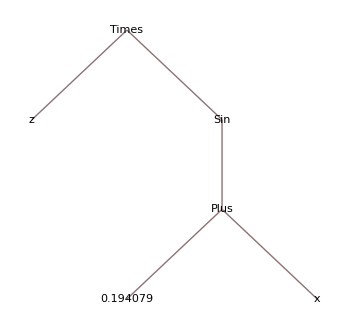

{0.194079+x}

Times

10

{{x,10},10}

<|Result:>1/2,Success→True,FailureType→None,OutputLog→{},Messages→{},MessagesText→{},MessagesExpressions→{},Timing→0.,AbsoluteTiming→0.,InputString:>ToString[Unevaluated[2/4],InputForm]|>

```mathematica
(* -- Everything is an expression -- *)

a = z*Sin[x+y];       (* don't display result with a semicolon; *)
FullForm[%]                   (* underlying full expression .. also //FullForm*)
TreeForm[a]                   (* tree form expression full levels *)
Level[a,{2}]                (* level 2 of the expression *)
Head[a]                            (* every expression has an head *)
x = Plus[Times[2,4],2] (* evaluate stuff also in full form .. (2*4)+2=10 *)
Trace[FullForm[x]]   (* internal evaluation dynamics *)

EvaluationData[2/4](* metadata about the process *)
```

```mathematica
(* Computation precision *)

SetPrecision[3/7,22]  (*for computation. btw do not use //N when set precision or will overwrite it*)
SetAccuracy[3/7,22]    (*for visual results*)
N[3/7,22]                           (*for numerical output.. same as for SetPrecision*)
Precision[0.42]               
(*MachinePrecision is generally 'double' aka 64bits yielding 16 decimal digits of mantissa*)
(*Numbers entered with a backtick ` but without a specified precision are treated as machine precision numbers...they are treated just like an undecorated number with a decimal point.A backtick without a number specifying precision is useful when applied to an integer without a decimal point. With a number having a decimal point,the backtick does nothing.*)
0.42`7

(* Temporarily change precision settings of global system parameters *)
Block[{$MaxPrecision=24,$MinPrecision=24},Sin[1`20]]

(* This estimates the worst precision loss in computing on the interval[0,1000] *)
100-Precision[BesselJ[1,RandomReal[{0,1000},1000,WorkingPrecision->100]]]
```

0.4285714285714285714286

0.428571428571428571429

0.4285714285714285714286

MachinePrecision

0.42

0.841470984807896506652502

5.52075

```mathematica
(* Evaluate an expression with a temporarily variable *)
Expand[(1+x)^5];
Block[{x=5},%]

With[{x=7},x^2]

(* If there is no need to assign to a local variable, a constant should be used instead *)
Timing[Do[Module[{x=5},x;],{10^5}]]

t=AbsoluteTime[];
Do[With[{x=5},x;],{10^5}]
AbsoluteTime[]-t
```

7776

49

{0.11586,Null}

0.043333

```mathematica
(* -- Pattern matching -- *)
Clear[f];
f[x_ ?EvenQ]:=x+2;   (* if x is even than engage this f *)
f[x_ ?OddQ]:=x^2;     (* if it's odd then this one *)
f[x_Integer]:=√(x;)   (* if it's an integer.. it'd never get here because of the above *)
f[x_]:= Sin[x];           (* if anything then go for this one *)
```

```mathematica
{f[2], f[3], f[g], f[9]}
```

{4,9,Sin[g],81}

```mathematica
(* -- Rules substitution -- *)

Clear[f,a,b];
f[a]+f[b] /. f[x_]->x^2  (* if anything, take the arg and square it *)
(* substitute (a) with a random number *)
Clear[sample,a,b,c,d,e,f,g,h];
sample={d,e,a,c,a,b,f,a,a,e,g,a};
sample /. a->Random[] (* a -> with the same random, Rule eval'ed once *)
sample /. a:>Random[]   (* a :> with different randoms.. RuleDelayed.. *)
sample /. a:>{Random[]+10} (* ... *)
```

a^2+b^2

{d,e,0.298401,c,0.298401,b,f,0.298401,0.298401,e,g,0.298401}

{d,e,0.650802,c,0.101051,b,f,0.956362,0.538603,e,g,0.658966}

{d,e,{10.5425},c,{10.9667},b,f,{10.8542},{10.5573},e,g,{10.1765}}

```mathematica
(* -- Symbols and evaluation -- *)

Clear[a];
Head[Jeez]                                              (* Any name which has a head Symbol is not used by the system *)
Head[a && True]                                   (* however Head check is after evaluation, so this is still a symbol .. *)
Head[Unevaluated[a && True]]      (* while for mathematica is an And which cannot be used as a symbol *)
?Jeez                         (* inspect a user defined symbol *)
?List                         (* inspect a build-in symbol  *)
```

Symbol

Symbol

And

```mathematica
(* -- Type definitions -- *)

(* actually there ain't no type def at all, values can be of any type any where *)
Clear[a,b];
a=3;
OwnValues[a]                    (* check if a value has been assigned to a proper var *)
b[1]=1; b[2]=3; 
OwnValues[b]                    (* no ownvalue that means we didn't stored stuff in an array here *)
DownValues[b]                  (* instead they are stored as downvalues, aka composite objects,   ie. indexed variables where indices can be any expr, hash tables are used to make indexed vars efficent *)
Clear[a,b,c,x,y,z];
a[b][1]=x;                       (* composite var are stored as SubValue global rule *)
a[b][2]=y;
a[c][1]=z;
SubValues[a]
```

{HoldPattern[a]:>3}

{}

{HoldPattern[b[1]]:>1,HoldPattern[b[2]]:>3}

{HoldPattern[a[b][1]]:>x,HoldPattern[a[b][2]]:>y,HoldPattern[a[c][1]]:>z}

```mathematica
(* -- Logical and conditional operators -- *)

Clear[a,b];
a=True;
b=False;

And[a,b]                (* And operator *)
a && b

Or[a,b]                  (* Or operator *)
a || b

If[a,10,-10]     (* If operator.. [condition, iftrue, iffalse] kinda like for C ternary op *)

TrueQ[b]
```

False

False

True

True

10

False

```mathematica
(* -- Loops constructors -- *)

For[i=0,i≤3,i++, Print[i]]  (* with regular comma, 0...6 *)
kk=For[i=0,i≤3,i++; Print[i]]  (* note the semicolon! 1...7 *)

jj="-----------"

For[i=1,i<3,i++,
For[j=1,j<3,j++, Print[i,"-",j]]
] (* nested loops *)

jj="-----------"

i=1;
While[i≤2, (Print[i]; i++)]     (*first test then eval evantually*)
While[procedure;test];                (*this is do-while.. evals proc _then_ go for test*)

jj="-----------"

i=1;
Do[Print[i]; If[i++>3, Break[]], {20}]  (* Break statement, Return will break one level up *)
(* there's also Goto and Continue to be used *)

(* Use Throw to exit a loop when a criterion is satisfied *)
Catch[Do[If[i!>10^10,Throw[i]],{i,100}]]
```

0

1

2

3

1

2

3

4

-----------

1-1

1-2

2-1

2-2

-----------

1

2

-----------

1

2

3

4

14

```mathematica
(* loops are inefficient! *)
i=1;
Timing[sm=0;
Do[sm=sm+1,{i,1000000}];sm]                       (* loop version *)

Timing[Apply[Plus, Range[1000000]]]              (* functional version *)

Compile[{x,{n,_Integer}},
Module[{sm=x},Do[sm=sm+i,{i,n}];sm]][0,1000000] //Timing                           (* but using internal compilation ... *)
```

{0.347014,1000000}

{0.128771,500000500000}

{0.015165,5.00001×10^11}

```mathematica
(* -- Lists -- *)

(* list are 1-based arrays *)
testlist = ConstantArray[1,32] (* insert 32 '1s' *)

testlist = {a,b,c,d,e,f}
testlist = Range[0,1,0.2]
testlist = Range[0,10,2]^2

Table[i*j, {i,1,2},{j,1,3}]     
Table[N[Sin[i]], {i,1,10}]
Table[Sin[i], {i,1,10}]                 (* better build list with tables than with loops *)

For[testlist={};i=1,i≤10,i++, testlist=Append[testlist, Sin[i]]];
testlist

testlist=Sin[Range[10]]  //N              (* same as above, but with Numbers *)
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{a,b,c,d,e,f}

{0.,0.2,0.4,0.6,0.8,1.}

{0,4,16,36,64,100}

{{1,2,3},{2,4,6}}

{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358,0.412118,-0.544021}

{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9],Sin[10]}

{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5],Sin[6],Sin[7],Sin[8],Sin[9],Sin[10]}

{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358,0.412118,-0.544021}

10

{1,4,7,10,13,16,19}

7

7

7

«1 more identical outputs»

{7,13,19}

{7,13,19}

{{5,6,7,8,9},{10,11,12,13,14},{15,16,17,18,19},{20,21,22,23,24},{25,26,27,28,29}}

11

11

{13,16,19}

{4,7,10,13}

{13,16,19}

{a,b,c,d,e,f,g,h}

{1,1,2,3,9}

{f[a],y,f[8],f[10]}

{{1,2},{5,4},{3,3}}

{0.822263,0.377567,0.287114,0.0720869,0.13651,0.938112,0.675368,0.792431,0.403034,0.129417,0.057381,0.825631}

{{0.822263,0.377567},{0.287114,0.0720869},{0.13651,0.938112},{0.675368,0.792431},{0.403034,0.129417},{0.057381,0.825631}}

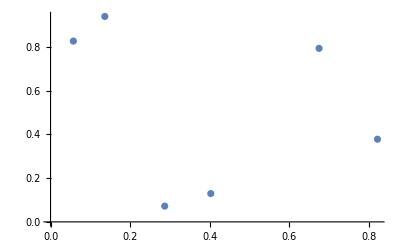

{0.0136096,0.0198216,0.076021,0.0950817,0.0984597,0.163677,0.337023,0.449687,0.45646,0.546775,0.664205,0.722281,0.744446,0.753569,0.763909,0.855099,0.869148,0.871201,0.874521,0.961603}

0.745283

{0.744446,0.753569}

{{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29,30},{31,32,33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48,49,50},{51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70},{71,72,73,74,75,76,77,78,79,80},{81,82,83,84,85,86,87,88,89,90},{91,92,93,94,95,96,97,98,99,100},{101,102,103,104,105,106,107,108,109,110},{111,112,113,114,115,116,117,118,119,120},{121,122,123,124,125,126,127,128,129,130},{131,132,133,134,135,136,137,138,139,140},{141,142,143,144,145,146,147,148,149,150}}

{55,155,255,355,455,555,655,755,855,955,1055,1155,1255,1355,1455}

{{2},{5},{6}}

{{2},{5},{6}}

```mathematica
(* workign with list and their parts *)
Clear[testlist];
testlist=Range[1,20,3]

testlist[[3]]                          (* extract third element *)
Part[testlist,3]
Extract[testlist,3]
testlist[[-5]]                        (* extract the fifth elem from the end *)


testlist[[{3,5,7}]]          (* extract third, fifth and seventh elems *)
Part[testlist, {3,5,7}]

complexlist=Range[5*#,5*#+4]&/@Range[5]  (* five lists of five elems each *)
complexlist[[2,2]]                                                           (* extract from list2 the 2nd element *)
Extract[complexlist,{2,2}]

Take[testlist,-3]              (* extract last 3 elems *)
Take[testlist, {2,5}]     (* extract from 2nd to 5th elem *)

Drop[testlist, 4]               (* extract from the 4th pos (not included) to the end *)

Flatten[{{a,b},{c,{d},e},{f,{g,h}}}]    (*flattens out nested lists; use it also for {} fnc returns *)

(* Cases *)
Cases[{1,1,f[a],2,3,y,f[8],9,f[10]},_Integer](*find cases that explicitly match integers*)
Cases[{1,1,f[a],2,3,y,f[8],9,f[10]},Except[_Integer]](*find cases that do not*)
Cases[{{1,2},{2},{3,4,1},{5,4},{3,3}},{_,_}](*find all cases of lists of two elements*)
Cases[data,{x_,y_}/;x^2+y^2<1];(*cases where x,y satisfy the equation.. /; condition op*)

(* Insert, Append, AppendTo, Prepend, PrependTo *)
(* ReplacePart[list, 1->0] , will make a copy of the original list !! *)
(* list[[1]=0 will just change the first elem with a zero *)

(* Let'say we have a bunch of random numbers and we wanna use them as 2d random points *)
Table[RandomReal[],{i,12}]
Partition[%,2](*group the flat list 2x2*)
ListPlot[%]

(* find the two nearest value in the list: one below and one above the input value *)
testlist =Sort[RandomReal[{0,1},20]]
ival = RandomReal[]
Sort[Nearest[testlist,ival,2,DistanceFunction->(Norm[#1-#2]&)]]

(* divide list into sublists *)
n=150;k=10;
lst=Range[n];
Partition[lst,10]
Map[Total,%]  (*get each chunck sum*)

(* find the position of matching vals from list to list *)
Position[{2,4,8,16,32,64},Alternatives@@{4,32,64}]
Flatten[Position[{2,4,8,16,32,64},#],1]&/@{4,32,64}
```

{{x→1/2 (-3-√17)},{x→1/2 (-3+√17)}}

{-3.56155,0.561553}

False

True

{2.,2.}==2

{2.,2.}==2

{True,True,False}

x==1/2 (-3-√17)||x==1/2 (-3+√17)

{{x→1/2 (-3-√17)},{x→1/2 (-3+√17)}}

{1/4 (-3-√17)^2+1/2 (-3-√17) a,1/4 (-3+√17)^2+1/2 (-3+√17) a}

{{x→0}}

a==0||x==0

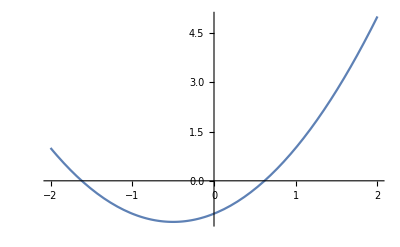

{{x→-(-1-2 b)/(a+b),y→-(-1+2 a)/(a+b)}}

{{x→5/4,y→-1/4}}

```mathematica
(* Equations *)

(*The Wolfram System treats equations as logical statements. If you type in an equation like x^2+3x==2,the Wolfram System interprets this as a logical statement that asserts that x^2+3x is equal to 2. 
If you assign an explicit value to x,say x=4,then the Wolfram System can explicitly determine that the logical statement x^2+3x==2 is False.*)

Solve[x^2+3 x==2,x](*solve for x*)
(*You can get a list of the actual solutions for x by applying the rules generated by Solve to x using the replacement operator*)
rList = x/.%//N 
(*If you replace x by the specific numerical value 4,the test gives False*)
x^2+3 x==2/.x->4
x^2+3 x==2/.x->%%[[1]] (*replace it with the first actual solution.. gives True*)

x^2+3 x==2/.x->rList (*replace it with the list of previous solutions.. confirm solution*)
ReplaceAll[x->rList][x^2+3 x==2] (*with operator form*)

AppendTo[rList,1.2];
Cases[rList,x_->x^2+3 x==2](*find what elem in the list satisfies the equation*)

Clear[x,a];
Reduce[x^2+3 x==2,x](*produce a logical statement about the values of x corresponding to the eq*)
{ToRules[%]}(*converted to transformation rules .. ->*)
x^2+a x/.%(*substitute the solutions for x into expressions involving x*)

(*A basic difference between Reduce and Solve is that Reduce gives all the possible solutions to a set of equations,while Solve gives only the generic ones.Solutions are considered "generic" if they involve conditions only on the variables that you explicitly solve for,and not on other parameters in the equations.Reduce and Solve also differ in that Reduce always returns combinations of equations,while Solve gives results in the form of transformation rules.*)
Clear[a,x];
Solve[a x==0,x](*if a≠0 then x->0 is the only solution*)
Reduce[a x==0,x](*if a==0 then any x is a solution*)

Plot[x+x^2==1,{x,-2,2}](*plot the evaluation of the equation with x values from -2 to +2*)

Clear[a,b,x,y];
Solve[{a x+b y==1,x-y==2},{x,y}](*a simple linear equation with two unknowns*)
Solve[{x+y==1,x-3 y==2}](*try to solve it for all variables*)
```

```mathematica
(* Functions *)

Clear[x,y,jeez]
jeez[x_Integer,y_Integer]/;(x>y):=x/y;
jeez[x__,y__]:=Print["jeez -> wrong argument(s) type"];
jeez[x__,y__]/;(!(x>y)):=Print["jeez -> X must be greater than Y"];

jeez[22,26]
jeez[22,"26"]
```

jeez -> X must be greater than Y

jeez -> wrong argument(s) type